```mathematica
file="D:\\Software\\Python Meas\\QControl_3.1\\onetone_phase.dat";
Import[file][[1]]
data=Import[file][[2;;]];
```

{freq,demod_Phase0,demod_Magnitude0}

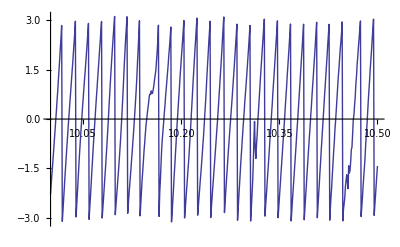

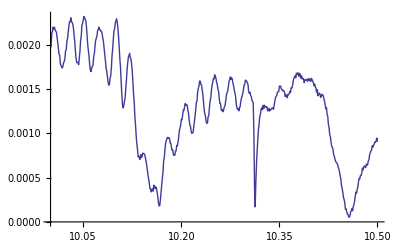

```mathematica
ListLinePlot[{#[[1]],#[[2]]}&/@data]
ListLinePlot[{#[[1]],#[[3]]}&/@data]
```

```mathematica
file="D:\\Software\\Python Meas\\QControl_3.1\\onetone_tight";
Import[file][[1]]
data=Import[file][[2;;]];
```

{freq,demod_Phase0,demod_Magnitude0}

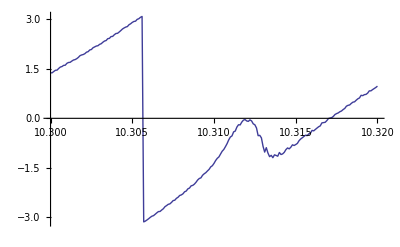

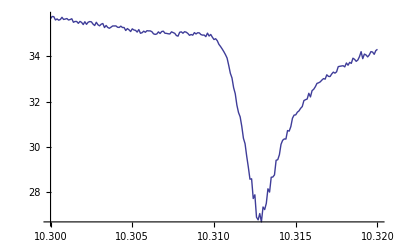

```mathematica
ListLinePlot[{#[[1]],#[[2]]}&/@data]
ListLinePlot[{#[[1]],-100*Log[#[[3]],10]}&/@data]
```

```mathematica
fileFreq0="D:\\Data\\Fluxonium #10\\One tune spectroscopy_YOKO 0mAto50mA_ qubit tone off_Cav_10p30GHz to 10p32GHz_1dBm_pulse_4000_2800_after 2nd thermal cycle_Freq.csv";
filePhase0="D:\\Data\\Fluxonium #10\\One tune spectroscopy_YOKO 0mAto50mA_ qubit tone off_Cav_10p30GHz to 10p32GHz_1dBm_pulse_4000_2800_after 2nd thermal cycle_Phase.csv";
fileMag0="D:\\Data\\Fluxonium #10\\One tune spectroscopy_YOKO 0mAto50mA_ qubit tone off_Cav_10p30GHz to 10p32GHz_1dBm_pulse_4000_2800_after 2nd thermal cycle_Mag.csv";
freq=Import[fileFreq0][[1]];
phase=Import[filePhase0][[1]];
mag=Import[fileMag0][[1]];
```

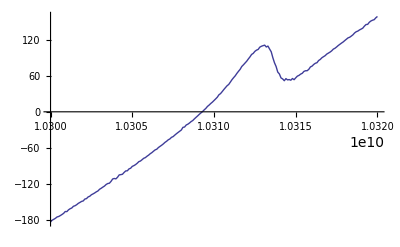

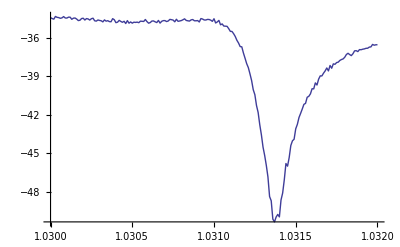

```mathematica
ListLinePlot[Transpose@{freq,phase}]
ListLinePlot[Transpose@{freq,mag}]
```